```mathematica
SetOptions[EvaluationNotebook[],PrintPrecision->Round[MachinePrecision]]
```

## Import Data

```mathematica
xdata={20,40,60,80,100,120,140,160,180,200};
ydata={33,30,27,26,23,20,19,17,18,12};
```

```mathematica
(*xdata={20,40,60,80,100,120,140,160,180,200};
ydata={36,33,30,28,25,22,21,19,19,13};*)
```

```mathematica
Length/@{xdata,ydata}
```

{10,10}

```mathematica
dy=Sqrt/@ydata//N
```

{5.74456,5.47723,5.19615,5.09902,4.79583,4.47214,4.3589,4.12311,4.24264,3.4641}

```mathematica
n=Length[xdata]
```

10

## Creating Table

```mathematica
Transpose[{xdata,ydata,Round[dy,0.1]}]//TeXForm//CopyToClipboard
```

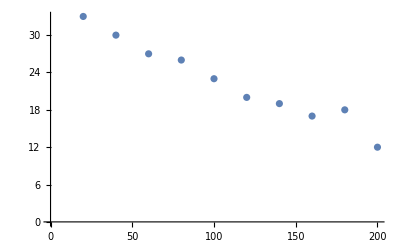

```mathematica
ListPlot[Transpose[{xdata,ydata}]]
```

```mathematica
logy=Log/@ydata//N
```

{3.49651,3.4012,3.29584,3.2581,3.13549,2.99573,2.94444,2.83321,2.89037,2.48491}

```mathematica
dlogy=Table[dy[[i]]/ydata[[i]],{i,1,Length[ydata]}]
```

{0.174078,0.182574,0.19245,0.196116,0.208514,0.223607,0.229416,0.242536,0.235702,0.288675}

```mathematica
Table[Log[Around[ydata[[i]],dy[[i]]]],{i,1,Length[ydata]}]
```

{3.500.17,3.400.18,3.300.19,3.260.20,3.140.21,3.000.22,2.940.23,2.830.24,2.890.24,2.480.29}

```mathematica
Transpose[{xdata,Round[logy,0.01],Round[dlogy,0.01]}]//TeXForm//CopyToClipboard
```

## Weighted Linear Regression

```mathematica
Δv2=Total[1/#^2&/@ dlogy]Sum[xdata[[i]]^2/dlogy[[i]]^2,{i,1,Length[xdata]}]-(Sum[xdata[[i]]/dlogy[[i]]^2,{i,1,Length[xdata]}])^2
```

1.57722×10^8

```mathematica
a2=1/Δv2 (Sum[logy[[i]]/dlogy[[i]]^2,{i,1,Length[logy]}] Sum[xdata[[i]]^2/dlogy[[i]]^2,{i,1,Length[logy]}]-Sum[xdata[[i]]/dlogy[[i]]^2,{i,1,Length[logy]}]Sum[xdata[[i]]logy[[i]]/dlogy[[i]]^2,{i,1,Length[logy]}])
```

3.5957

```mathematica
b2=1/Δv2(Total[1/#^2&/@ dlogy]Sum[xdata[[i]]logy[[i]]/dlogy[[i]]^2,{i,1,Length[logy]}]-Sum[xdata[[i]]/dlogy[[i]]^2,{i,1,Length[logy]}]Sum[logy[[i]]/dlogy[[i]]^2,{i,1,Length[logy]}])
```

-0.00469591

```mathematica
da1=Sqrt[1/Δv2 Sum[xdata[[i]]^2/dlogy[[i]]^2,{i,1,Length[logy]}]]
```

0.131168

```mathematica
db2=Sqrt[1/Δv2 Total[1/#^2&/@ dlogy]]
```

0.00119439

```mathematica
-Log[2]/b2
```

147.607

```mathematica
Log[2]/b2^2 db2
```

37.5433

```mathematica
fit=NonlinearModelFit[Transpose[{xdata,logy}],a + b x,{a,b},x,Weights->1/dlogy^2]
```

FittedModel[…]

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 3.5957 | 0.0411172 | 87.45 | 3.26215×10^-13
b | -0.00469591 | 0.000374406 | -12.5423 | 1.52972×10^-6

```mathematica
tab=fit["ParameterTableEntries"]
```

{{3.5957,0.0411172,87.45,3.26215×10^-13},{-0.00469591,0.000374406,-12.5423,1.52972×10^-6}}

```mathematica
CDF[NormalDistribution[]][da1/tab[[1,2]]]
```

0.999289

```mathematica
CDF[NormalDistribution[]][da1/tab[[1,2]]]-CDF[NormalDistribution[]][-da1/tab[[1,2]]]
```

0.998578

```mathematica
Sqrt[n]//N
```

3.16228

```mathematica
da1/tab[[1,2]]
```

3.19009

```mathematica
db2/tab[[2,2]]
```

3.19009